# Teoría de Autómatas y Lenguajes Formales

## Clase 12 - Máquinas de Turing 2

Profesor: Tomás de Camino Beck, Ph.D.

tomas.decamino@gmail.com

## Introducción

Mathematica permite utilizar códigos numéricos para representar Máquinas de Turing. De esa manera entonces puede representar MT,

| 2-state, 2-color machines | 4096
       | s-state, k-color machines | (2 s k)^(s k)
       | s-state, k-color, range-r machines | (2 r s k)^(s k)
       | 2D s-state, k-color machines | (8 s k)^(s k)

Con “Color” se refiere a símbolos del alfabeto de la MT. Con la función RulePlot podemos ver una bonita representación de las reglas definidas numéricamente,

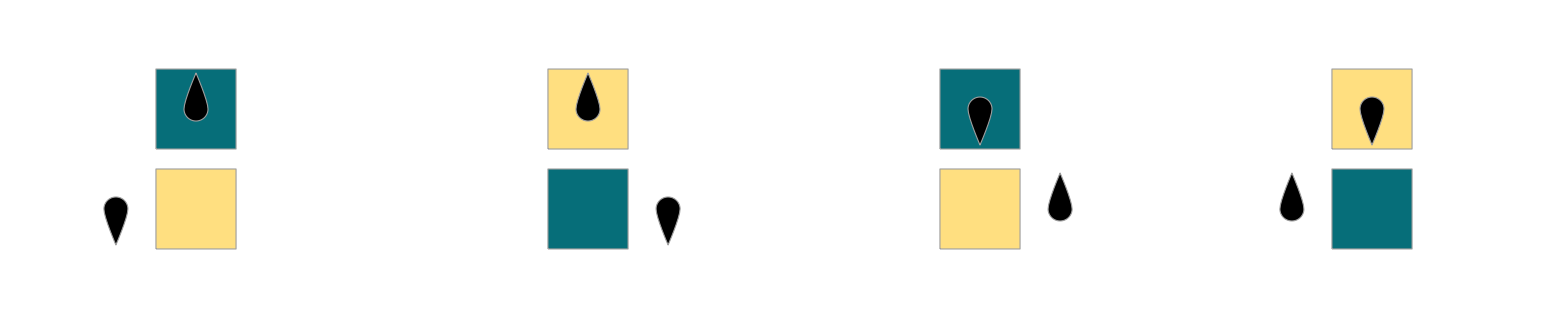

```mathematica
RulePlot[TuringMachine[2506]]
```

Esto representa una MT de 2 estados y 2 símbolos (colores). La primera línea representa las 4 posibilidades de estado y símbolo en la que la cabeza de la MT se puede encontrar, y la segunda línea la transición. Así por ejemplo la primera regla (de derecha a izquierda),

lo que indica es que cuando la cabeza está en estado 1 (), con el símbolo , pasa a estado 0 (), escribe el símbolo  y se mueve a la izquierda.

Cada tripleta representa  donde  es estado {0,1} ,  es símbolo (color), y  es dirección 0 izquierda y 1 derecha. Es decir se representa la transición (q,X)=(p,Y,D) descrita en Hopcroft, escrito como , de la siguiente manera,

{0,1} | {0,0} | {1,1} | {1,0}
{1,0,0} | {1,1,1} | {0,0,1} | {0,1,0}

Si tomamos la segunda línea {{1,0,0} | {1,1,1} | {0,0,1} | {0,1,0}}y desagregamos las tripletas,

```mathematica
Flatten[{{1,0,0},{1,1,1},{0,0,1},{0,1,0}}]
```

{1,0,0,1,1,1,0,0,1,0,1,0}

Luego convertimos a número entero base 10,

```mathematica
FromDigits[{1,0,0,1,1,1,0,0,1,0,1,0},2]
```

2506

Obtendremos la codificación en binario de la regla.  Esta misma regla la podemos escribir en formato de reglas,

```mathematica
rules={
{0,1}-> {1,0,-1},
{0,0}->  {1,1,1},
{1,1}-> {0,0,1},
{1,0}-> {0,1,-1}
};
```

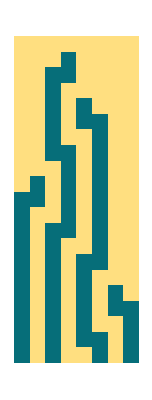

```mathematica
ArrayPlot[Last /@ TuringMachine[rules, {1, {{}, 0}}, 20]]
```

Que es lo mismo que la regla 2506,

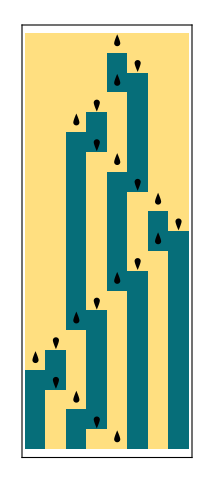

```mathematica
RulePlot[TuringMachine[2506], {1, {{}, 0}}, 20]
```

La ventaja está en la representación gráfica muestra la posición de la cabeza, además de la cinta.

## Explorando muchas MT

La ventaja de la codificación de una MT como número entero, es que se puede explorara el comportamiento de muchas MT. Así por ejemplo podemos explorar MT de dos estados y 2 símbolos como,

```mathematica
Table[RulePlot[TuringMachine[i],{1,{{},0}},20,ImageSize-> {30,30}],{i,2000,2500}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Gráficamente no todas las MT generan resultados interesantes.

## Funciones Utilizadas

TuringMachinepaclet:ref/TuringMachine[rule,init,t]
generates a list representing the evolution of the Turing machine with the specified rule from initial condition init for t steps.

RulePlotpaclet:ref/RulePlot[sys,init,t]
generates a plot of the evolution of the system sys from initial condition init for t steps.

RulePlotpaclet:ref/RulePlot[sys] 
generates a plot representing the rule for the computational system sys.

FromDigitspaclet:ref/FromDigits[list,b]
takes the digits to be given in base b.

ArrayPlotpaclet:ref/ArrayPlot[array]
generates a plot in which the values in an array are shown in a discrete array of squares.